```mathematica
$Assumptions={d > 0, kx ∈ Reals, ky ∈ Reals, t ∈ Reals, t>0, qx ∈ Reals, qy ∈ Reals, θ ∈ Reals, ϵx ∈ Reals, ϵy ∈ Reals, ϵ ∈ Reals, ϵ > 0, tp >0}
```

{d>0,kx∈ℝ,ky∈ℝ,t∈ℝ,t>0,qx∈ℝ,qy∈ℝ,θ∈ℝ,ϵx∈ℝ,ϵy∈ℝ,ϵ∈ℝ,ϵ>0,tp>0}

```mathematica
δ = {{0, d}, {d Cos[30 Degree], - d Sin[30 Degree]}, {-d Cos[30 Degree], - d Sin[30Degree]}}
```

{{0,d},{(√3 d)/2,-d/2},{-(√3 d)/2,-d/2}}

```mathematica
f[k_] := - t * Sum[Exp[I  k . δ[[i]]], {i, 1, 3}]
```

```mathematica
H[k_] := {{0, -t Sum[Exp[-I k.δ[[i]]], {i, 1, 3}]}, {-t Sum[Exp[I k.δ[[i]]], {i, 1, 3}], 0}}
```

```mathematica
h[k_]:= -{ComplexExpand[Re[f[k]]], ComplexExpand[Im[f[k]]]}/t
```

```mathematica
K = {4 Pi/(3 Sqrt[3] d), 0}
```

{(4 π)/(3 √3 d),0}

```mathematica
FullSimplify[Norm[h[{kx, ky}]]]
```

√(3+2 Cos[√3 d kx]+2 Cos[1/2 d (√3 kx-3 ky)]+2 Cos[1/2 d (√3 kx+3 ky)])

```mathematica
FullSimplify[Series[Series[FullSimplify[f[K + {ϵx, ϵy}]],{ϵy, 0, 1}], {ϵx, 0, 1}]] // Normal
```

(3 d t ϵx)/2+(-3/2 ⅈ d t-3/4 ⅈ d^2 t ϵx) ϵy

```mathematica
linf[{ϵx_, ϵy_}] := (3 d t ϵx)/2-3/2 ⅈ d t ϵy
```

```mathematica
linH[{ϵx_, ϵy_}] := {{0, Conjugate[linf[{ϵx, ϵy}]]}, {linf[{ϵx, ϵy}], 0}}
```

```mathematica
FullSimplify[linH[{ϵx, ϵy}]] //MatrixForm
```

(0 | 3/2 d t (ϵx+ⅈ ϵy)
3/2 d t (ϵx-ⅈ ϵy) | 0)

```mathematica
{{Em, Ep}, {um, up}}  = FullSimplify[Eigensystem[{{0,3/2 d t (ϵx+ⅈ ϵy)},{3/2 d t (ϵx-ⅈ ϵy),0}}] ]
```

{{-3/2 d t √(ϵx^2+ϵy^2),3/2 d t √(ϵx^2+ϵy^2)},{{-(ϵx+ⅈ ϵy)/(√(ϵx^2+ϵy^2)),1},{(ϵx+ⅈ ϵy)/(√(ϵx^2+ϵy^2)),1}}}

```mathematica
FullSimplify[Conjugate[up].D[up, ϵy]]
```

(ⅈ ϵx)/(ϵx^2+ϵy^2)

```mathematica
Residue[-i/z, {z, 0}]
```

-i

```mathematica
fp[k_] :=  - t * Sum[Exp[I  k . δ[[i]]], {i,2, 3}]  - tp * Sum[Exp[I  k . δ[[i]]], {i,1, 1}]
```

```mathematica
FullSimplify[fp[{kx, ky}]]
```

-ⅇ^(-1/2 ⅈ d (√3 kx+ky)) (t+ⅇ^(ⅈ √3 d kx) t+ⅇ^(1/2 ⅈ d (√3 kx+3 ky)) tp)

```mathematica
hp[k_]:= -{ComplexExpand[Re[fp[k]]], ComplexExpand[Im[fp[k]]]}
```

```mathematica
FullSimplify[Norm[hp[{kx, ky}]]]
```

√(2 t^2+tp^2+2 t (t Cos[√3 d kx]+tp (Cos[1/2 d (√3 kx-3 ky)]+Cos[1/2 d (√3 kx+3 ky)])))

```mathematica
M = {0, 2 Pi/(3 d)}
```

{0,(2 π)/(3 d)}

```mathematica
linfp[ϵx_, ϵy_, t_, tp_, d_] := (-1)^(1/6) (2 ⅈ t-ⅈ tp+d (t+tp) ϵy)
```

```mathematica
H = FullSimplify[{{0, Conjugate[linfp]}, {linfp, 0}}]
```

{{0,-(-1)^(5/6) (-2 ⅈ t+ⅈ tp+d (t+tp) ϵy)},{(-1)^(1/6) (2 ⅈ t-ⅈ tp+d (t+tp) ϵy),0}}

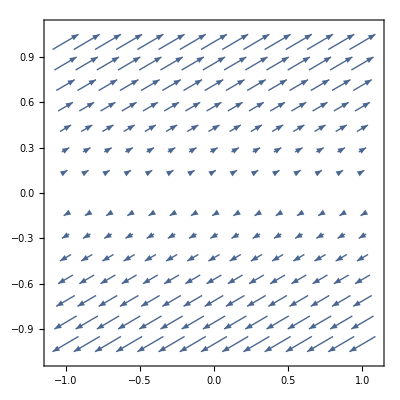

```mathematica
VectorPlot[{Re[linfp[ϵx, ϵy, 1, 2, 1]], Im[linfp[ϵx, ϵy, 1, 2, 1]]}, {ϵx, -1, 1}, {ϵy, -1, 1}]
```

```mathematica
FullSimplify[ComplexExpand[Eigenvectors[H]]]
```

{{-(ⅇ^(1/2 ⅈ Arg[-(-1)^(2/3) ((-2 t+tp)^2+d^2 (t+tp)^2 ϵy^2)]) √((-2 t+tp)^2+d^2 (t+tp)^2 ϵy^2))/(2 ⅈ t-ⅈ tp+d (t+tp) ϵy),1},{(ⅇ^(1/2 ⅈ Arg[-(-1)^(2/3) ((-2 t+tp)^2+d^2 (t+tp)^2 ϵy^2)]) √((-2 t+tp)^2+d^2 (t+tp)^2 ϵy^2))/(2 ⅈ t-ⅈ tp+d (t+tp) ϵy),1}}

```mathematica
PauliMatrix[3]
```

{{1,0},{0,-1}}

```mathematica
ComplexExpand[(a + I b)(c + I d)]
```

a c-b d+ⅈ (b c+a d)

```mathematica
ComplexExpand[(a - I b)(c + I d)]
```

a c+b d+ⅈ (-b c+a d)